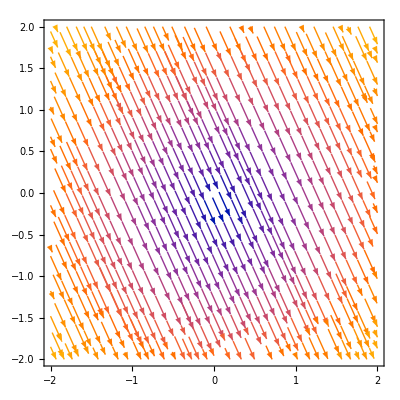

```mathematica
Clear["Global`*"]
minx = -2;
miny = -2;
maxx = 2;
maxy = 2;
tmin = -10;
tmax = 10;
dist = 0.1;


(*
f = {y-x,x^2};
sol[x0_,y0_] := NDSolve[
{x'[t]==y[t]-x[t],
y'[t]==x[t]^2,
x[0]==x0,y[0]==y0},
{x,y},{t,tmin,tmax}]
*)


(*
f = {y^3,x};
sol[x0_,y0_] := NDSolve[
{x'[t]==y[t]^3,
y'[t]==x[t],
x[0]==x0,y[0]==y0},
{x,y},{t,tmin,tmax}]
*)
a = -4;
θ = 2;
f = {a*Sqrt[x^2+y^2]*Cos[θ],a*Sqrt[x^2+y^2]*Sin[θ]};
sol[x0_,y0_] := NDSolve[
{x'[t]==a*Sqrt[x[t]^2+y[t]^2]*Cos[θ],
y'[t]==a*Sqrt[x[t]^2+y[t]^2]*Sin[θ],
x[0]==x0,y[0]==y0},
{x,y},{t,tmin,tmax}]

(*
n= -6;
f = {(x^2+y^2)^(Abs[n]/2)*Cos[n*ArcTan[y/x]],(x^2+y^2)^(Abs[n]/2)*Sin[n*ArcTan[y/x]]};
sol[x0_,y0_] := NDSolve[
{x'[t]==(x[t]^2+y[t]^2)^(Abs[n]/2)*Cos[n*ArcTan[y[t]/x[t]]],
y'[t]==(x[t]^2+y[t]^2)^(Abs[n]/2)*Sin[n*ArcTan[y[t]/x[t]]],
x[0]==x0,y[0]==y0},
{x,y},{t,tmin,tmax}]
*)


initialCond = Join[
Table[{x , miny},{x , minx , maxx,dist}],
Table[{x,maxy},{x,minx , maxx,dist}],
Table[{minx , y } , {y,miny , maxy,dist}],
Table[{maxx, y} , {y, miny , maxy,dist}]
];

(*ParametricPlot[
Evaluate[{x[t],y[t]}/. sol[initialCond[[50,1]],initialCond[[50,2]]]],
{t,tmin,tmax}, PlotRange->{{minx,maxx},{miny,maxy}}]*)

(*p0 = Show[
(*Table[
ParametricPlot[
Evaluate[{x[t], y[t]}/.sol[initialCond[[i,1]], initialCond[[i,2
]]]],{t,tmin,tmax},PlotRange->{{minx,maxx},{miny,maxy}}],{i,1,Length[initialCond]}],*)
StreamPlot[f,{x,minx,maxx},{y,miny,maxy},StreamPoints->{Automatic 0.01},PlotRange->{{minx,maxx},{miny,maxy}}]&/@{1,0.3,0.1,0.03,0.01}
];*)
StreamPlot[f,{x,minx,maxx},{y,miny,maxy},StreamPoints->{Automatic,0.1}]
```

```mathematica
Clear[x,y,f1,f2,f3,f4,min,max]
min=-1;
max = 1;

(*
n =1;
f1 = ArcTan[Tan[n*ArcTan[y]]];
f2 = ArcTan[Tan[n*ArcTan[1/x]]];
f3 = ArcTan[Tan[n*ArcTan[-y]]];
f4 = ArcTan[Tan[n*ArcTan[-1/x]]];
*)
f1 = ArcTan[1/y^3];
f2 = ArcTan[x];
f3 = ArcTan[-1/y^3];
f4 = ArcTan[-x];

(*ansD = 1/(2*π)*(Integrate[f1,{y,min,max}]+Integrate[f2,{x,max,min}])+Integrate[f3,{y,max,min}]+Integrate[f4,{x,min,max}])//FullSimplify*)
ansD = 1/(2*π)*(Integrate[f1,y]+Integrate[f2,x]+Integrate[f3,y]+Integrate[f4,x])//FullSimplify;
```

0